```mathematica
Manipulate[
Module[{C1,C2,χ,kc1,kc2,Π,nA,C1i,C2i,C1is,C2is,d},
C1=0.03;C2=0.005;(*kmol/m3*)
kc1=4*^-5;kc2=2*^-5;(*m/s*)
χ=DA/100^2;(*m2/s*)

Π[z_]:=(χ*k)/z;
nA[z_]:=(C1-C2)/(1/kc1+1/Π[z]+1/kc2);

C1i[z_]:=C1-nA[z]/kc1;
C2i[z_]:=C2+nA[z]/kc2;
C1is[z_]:=k*C1i[z];
C2is[z_]:=k*C2i[z];

Show[
Plot[{C1is[z],C2is[z]},{z,0,L},PlotStyle->{{Thick,Red},{Thick,Dashed,Red}}],
Plot[{C1i[z],C2i[z]},{z,0,L},PlotStyle->{{Thick,Blue},{Thick,Dashed,Blue}}],
PlotRange->All];

Plot[C1i[z],{z,-0.5*L,L}]
],
Control[{{DA,0.7,Row@{"diffusion constant (",Superscript["cm",2],"/s)"}},0.2,0.95,0.05,Appearance->"Labeled"}],
Control[{{L,10,"membrane thickness (m)"},1,20,1,Appearance->"Labeled"}],
Control[{{k,1.5,"equilirium constant"},0.5,2,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{C1,C2,χ,kc1,kc2,Π,nA,C1i,C2i,C1is,C2is,d},
C1=0.03;C2=0.005;(*kmol/m3*)
kc1=4*^-5;kc2=2*^-5;(*m/s*)
χ=DA/100^2;(*m2/s*)

Π=(χ*k)/L;
nA=(C1-C2)/(1/kc1+1/Π+1/kc2);

C1i=C1-nA/kc1;
C2i=C2+nA/kc2;
C1is=k*C1i;
C2is=k*C2i;

(*d=1*^3*L;*)d=Max[{C1i,C2i,C1is,C2is}]/1.8;

(*Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{d,1.2*Max@{C1i,C2i,C1is,C2is}}]},
{Thick,Line[{{-0.5*d,C1},{0,C1i}}],Line[{{d,C2i},{1.5*d,C2}}],Line[{{0,C1is},{d,C2is}}]},
{PointSize@0.02,Point@{-0.5*d,C1},Point@{0,C1i},Point@{d,C2i},Point@{1.5*d,C2},Point@{0,C1is},Point@{d,C2is}}
},ImageSize->{600,450},Frame->True];*)
Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{d,0.062}]},
{Thick,(*Line[{{-0.5*d,C1},{0,C1i}}],Line[{{d,C2i},{1.5*d,C2}}],*)
BezierCurve@{{-0.5*d,C1},{-0.05*d,1.05*C1},{0,C1i}},BezierCurve@{{d,C2i},{1.05*d,0.95*C2},{1.5*d,C2}},
Line[{{0,C1is},{d,C2is}}]},
{PointSize@0.02,Point@{-0.5*d,C1},Point@{0,C1i},Point@{d,C2i},Point@{1.5*d,C2},Point@{0,C1is},Point@{d,C2is}},
{Thick,Arrowheads@{-0.04,0.04},Arrow[{{0,0.06},{d,0.06}}]},
Text[Style[" L ",18,Italic,Background->White],{d/2,0.06}],
(*{Thick,Red,BezierCurve@{{-0.5*d,C1},{-0.05*d,1.05*C1},{0,C1i}},BezierCurve@{{d,C2i},{1.05*d,0.95*C2},{1.5*d,C2}}}*)
Text[Style[Subscript[Style["C",Italic],#1],18],#2,1.5*#3]&@@@{
{1,{-0.5*d,C1},{1,0}},{2,{1.5*d,C2},{-1,0}},{"1,i",{0,C1i},{-1,0}},{"2,i",{d,C2i},{1,0}},{"1,i,s",{0,C1is},{1,0}},{"2,i,s",{d,C2is},{-1,0}}}
},ImageSize->{600,400},PlotRange->{{-0.016,0.049},All}]
],
Control[{{DA,0.7,Row@{"diffusion constant (",Superscript["cm",2],"/s)"}},0.2,0.95,0.05,Appearance->"Labeled"}],
Control[{{L,10,"membrane thickness (m)"},1,20,1,Appearance->"Labeled"}],
Control[{{k,1.5,"equilirium constant"},0.5,2,0.1,Appearance->"Labeled"}]
]
```

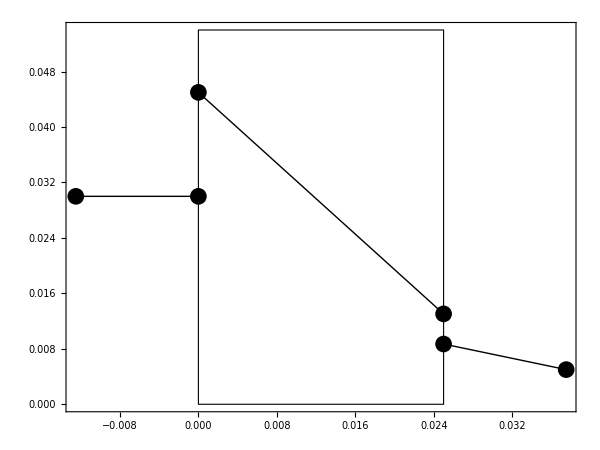

```mathematica
Module[{C1,C2,L,k,kc1,kc2,χ,Π,nA,C1i,C2i,C1is,C2is,d},
C1=0.03;C2=0.005;(*kmol/m3*)
L=3*^-5;(*m*)
k=1.5;kc1=100;kc2=2.02*^-5;(*m/s*)
χ=7*^-11;(*m2/s*)

Π=(χ*k)/L;
nA=(C1-C2)/(1/kc1+1/Π+1/kc2);

C1i=C1-nA/kc1;
C2i=C2+nA/kc2;
C1is=k*C1i;
C2is=k*C2i;

(*d=1*^3*L;*)d=Max[{C1i,C2i,C1is,C2is}]/1.8;

Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{d,1.2*Max@{C1i,C2i,C1is,C2is}}]},
{Thick,Line[{{-0.5*d,C1},{0,C1i}}],Line[{{d,C2i},{1.5*d,C2}}],Line[{{0,C1is},{d,C2is}}]},
{PointSize@0.02,Point@{-0.5*d,C1},Point@{0,C1i},Point@{d,C2i},Point@{1.5*d,C2},Point@{0,C1is},Point@{d,C2is}}
},ImageSize->{600,450},Frame->True]
]
```